## Trabajo práctico final - Ecuación de Schrödinger

Pablo Chehade
Inicio: 01/12/2021
Última actualización: 18/12/2021

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Parámetros del problema: *)
J = 1000;
Nt = 2138;
(*Valores para Nt por inciso:;
1. 4501;
2.i. 6047;
2.ii. 3054;
2.iii. 2138;
*)
epsilon=0.001;
delta = 2*epsilon *epsilon;
L = 1;
k0 = "25√2π"; (*solo para graficar, sin el PI*)
datos = "2.iii."; (*datos de qué inciso voy a cargar*)
(*Cargo los datos: *)
archivos = {"G:/Mi unidad/Pablo Chehade/Instituto Balseiro (IB)/Introducción a Física Computacional - FISCOM/Trabajos prácticos/TP Final/Schrodinger_v1/Datos/" <> datos <> "malla_real.dat",
"G:/Mi unidad/Pablo Chehade/Instituto Balseiro (IB)/Introducción a Física Computacional - FISCOM/Trabajos prácticos/TP Final/Schrodinger_v1/Datos/" <> datos <> "malla_imag.dat",
"G:/Mi unidad/Pablo Chehade/Instituto Balseiro (IB)/Introducción a Física Computacional - FISCOM/Trabajos prácticos/TP Final/Schrodinger_v1/Datos/" <> datos <> "valores_medios_real.dat", "G:/Mi unidad/Pablo Chehade/Instituto Balseiro (IB)/Introducción a Física Computacional - FISCOM/Trabajos prácticos/TP Final/Schrodinger_v1/Datos/" <> datos <> "valores_medios_imag.dat"};
datosReal = Import[archivos⟦1⟧, "FieldSeparators"->"\t"];
datosImag = Import[archivos⟦2⟧, "FieldSeparators"->"\t"];
datosValoresMediosReal =  Import[archivos⟦3⟧, "FieldSeparators"->"\t"];
datosValoresMediosImag = Import[archivos⟦4⟧, "FieldSeparators"->"\t"];

(*La malla está cargada como una matriz donde cada componente es un vector formado por la parte real y la parte compleja del nro. Paso todo a una matriz compleja: *)
malla = ConstantArray[0,{J,Nt}];
Do[
Do[
malla⟦j,n⟧ = datosReal⟦j,n⟧ + I datosImag⟦j,n⟧;
,{j,1,J}],{n,1,Nt}]

Energy = ConstantArray[0, Nt];
Norma = ConstantArray[0, Nt];
xMean = ConstantArray[0,Nt];
xVar = ConstantArray[0, Nt];
pMean = ConstantArray[0,Nt];
p2Mean = ConstantArray[0,Nt];
pVar = ConstantArray[0, Nt];
Do[
Energy⟦n⟧ = datosValoresMediosReal⟦1,n⟧ + I datosValoresMediosImag⟦1,n⟧;
Norma⟦n⟧ = datosValoresMediosReal⟦2,n⟧ + I datosValoresMediosImag⟦2,n⟧;
xMean⟦n⟧ = datosValoresMediosReal⟦3,n⟧ + I datosValoresMediosImag⟦3,n⟧;
xVar⟦n⟧ = datosValoresMediosReal⟦4,n⟧ + I datosValoresMediosImag⟦4,n⟧;
pMean⟦n⟧ = datosValoresMediosReal⟦5,n⟧ + I datosValoresMediosImag⟦5,n⟧;
p2Mean⟦n⟧ = datosValoresMediosReal⟦6,n⟧ + I datosValoresMediosImag⟦6,n⟧;
pVar⟦n⟧ = datosValoresMediosReal⟦7,n⟧ + I datosValoresMediosImag⟦7,n⟧;
,{n,1,Nt}]

tmax = Length[Energy]*delta;
(*Ticks eje t y x*)
tLista = Table[n,{n,0,Nt-1}];
xLista  =  Table[j*epsilon,{j,0,J-1}];

(*Por alguna razón que desconozco, el código de C++ calcula mal la varianza de p, así que la vuelvo a calcular acá:*)
Do[pVar⟦n⟧ = Abs[p2Mean⟦n⟧] - Abs[pMean⟦n⟧]^2;,{n,1,Nt}];
```

### Evolución temporal

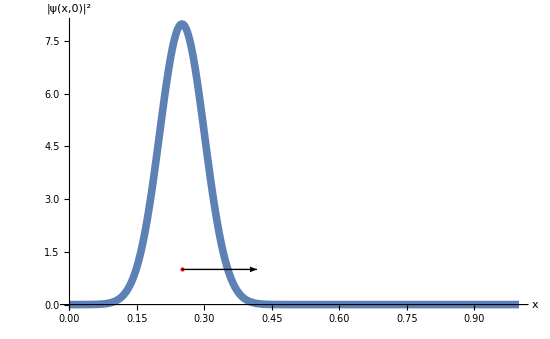

```mathematica
(*Condición inicial*)
x =xLista;
PhiInicial = malla⟦;;,1⟧;
ProbInicial = Abs[PhiInicial*Conjugate[PhiInicial]];IniGraph = ListPlot[Transpose[{x,ProbInicial}], PlotRange->All,  AxesLabel->{"x", "|ψ(x,0)|^2"}, AxesStyle->Large, Joined->True , Mesh->None, PlotStyle->{Thickness[0.01]}];
(*Grafico xMean*)
xMeanPoint = Graphics[{PointSize[Large],Red,Point[{Re[xMean⟦1⟧],1}]}];
(*Grafico pMean representándolo como una flecha de módulo igual a pMean escaleado por el máximo de pMean alcanzado*)
pnorma =Abs[pMean⟦1⟧];
pfinal = Re[pMean⟦1⟧]/(6*pnorma);
pMeanArrow = Graphics[Arrow[{{Re[xMean⟦1⟧],1},{pfinal + Re[xMean⟦1⟧],1}}]];
Show[{IniGraph, xMeanPoint, pMeanArrow}]

(*Evolución temporal*)

grafica[n_,pot_]:=Module[{graph, point, pnorma, pfinal, arrow,pot1,pot2,pot3,a,altura,x1,x2},
(*Grafico Phi: *)
graph= ListPlot[Transpose[{x,malla⟦;;,n⟧*Conjugate[ malla⟦;;,n⟧]}],PlotRange->{{0,L},{0,Max[ProbInicial]+1}},  AxesLabel->{"x", "ψ(x,t)"}, AxesStyle->Large, Joined->True , Mesh->None, PlotStyle->{Thickness[0.01]}, Epilog->{Inset[Style["k_0="<>k0<>"\nt="<>ToString[n*epsilon],15,Background->White],{0.9,Max[ProbInicial]-0.3}]}];
(*Grafico xMean*)
point = Graphics[{PointSize[Large],Red,Point[{Re[xMean⟦n⟧],1}]}];
(*Grafico pMean representándolo como una flecha de módulo igual a pMean escaleado por el máximo de pMean alcanzado*)
pnorma = Max[Abs[pMean]];
pfinal = Re[pMean⟦n⟧]/(6*pnorma);
arrow = Graphics[Arrow[{{Re[xMean⟦n⟧],1},{pfinal + Re[xMean⟦n⟧],1}}]];
(*Grafico el potencial:*)
If[pot==True, 
a = 0.032;
altura = 0.6*Max[ProbInicial];
x1 = L/2 - a;
x2 = L/2 +a;
pot1 = ListPlot[{{x1,0},{x1,altura}}, Joined->True, PlotStyle->{Thickness[0.01], Orange}];
pot2 = ListPlot[{{x1,altura},{x2,altura}}, Joined->True, PlotStyle->{Thickness[0.01], Orange}];
pot3 = ListPlot[{{x2,0},{x2,altura}}, Joined->True, PlotStyle->{Thickness[0.01], Orange}];
Show[{graph,point, arrow,pot1,pot2,pot3}],
Show[{graph,point, arrow}]]
]

Manipulate[
grafica[n,False]
,{n,1,Nt,1}]
```

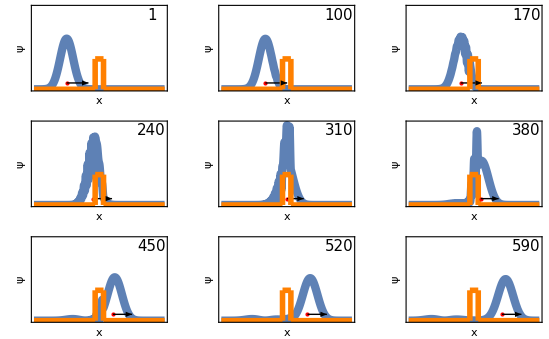

```mathematica
(*Grafico a varios tiempos*)
GraficaConjunta[n_,pot_]:=Module[{graph, point, pnorma, pfinal, arrow,a,altura,x1,x2,pot1,pot2,pot3},
(*Grafico Phi: *)
graph= ListPlot[Transpose[{x,malla⟦;;,n⟧*Conjugate[ malla⟦;;,n⟧]}],PlotRange->{{0,L},{0,1.5*Max[ProbInicial]+1}},  AxesLabel->{"x", "ψ"}, AxesStyle->Large, Joined->True , Mesh->None, PlotStyle->{Thickness[0.015]}, Axes->False, Frame->True,
Epilog->{Inset[Style[ToString[n],15,Background->White],{0.9,1.5*Max[ProbInicial]-0.3}]}, PlotTheme->"Minimal"];
(*Grafico xMean*)
point = Graphics[{PointSize[Large],Red,Point[{Re[xMean⟦n⟧],1}]}];
(*Grafico pMean representándolo como una flecha de módulo igual a pMean escaleado por el máximo de pMean alcanzado*)
pnorma = Max[Abs[pMean]];
pfinal = Re[pMean⟦n⟧]/(6*pnorma);
arrow = Graphics[Arrow[{{Re[xMean⟦n⟧],1},{pfinal + Re[xMean⟦n⟧],1}}]];
If[pot==True, 
a = 0.032;
altura = 0.6*Max[ProbInicial];
x1 = L/2 - a;
x2 = L/2 +a;
pot1 = ListPlot[{{x1,0},{x1,altura}}, Joined->True, PlotStyle->{Thickness[0.01], Orange}];
pot2 = ListPlot[{{x1,altura},{x2,altura}}, Joined->True, PlotStyle->{Thickness[0.01], Orange}];
pot3 = ListPlot[{{x2,0},{x2,altura}}, Joined->True, PlotStyle->{Thickness[0.01], Orange}];
pot4=ListPlot[{{0,0},{x1,0}}, Joined->True, PlotStyle->{Thickness[0.01], Orange}];
pot5=ListPlot[{{x2,0},{1,0}}, Joined->True, PlotStyle->{Thickness[0.01], Orange}];
Show[{graph,point, arrow,pot1,pot2,pot3,pot4, pot5}],
Show[{graph,point, arrow}]]
]
pot = True;
ns ={1,100,170,240,310,380,450,520, 590};
(*ns para cada inciso:;
ns1 = {1,600,1000,1500,2200,2500,2900,3500,4000};
ns2i ={1,150,300,450,600,850,1000,1150,1350};
ns2ii ={1,150,220,290,370,500,600,700,850};
ns2iii ={1,100,170,240,310,380,450,520, 590};

ns son los instantes de tiempo que grafico para representar la evolución de la función de onda en el tiempo
*)

(*Gráfico conjunto: *)
p1 = GraficaConjunta[ns⟦1⟧,pot];
p2 = GraficaConjunta[ns⟦2⟧,pot];
p3 = GraficaConjunta[ns⟦3⟧,pot];
p4 = GraficaConjunta[ns⟦4⟧,pot];
p5 = GraficaConjunta[ns⟦5⟧,pot];
p6 = GraficaConjunta[ns⟦6⟧,pot];
p7 = GraficaConjunta[ns⟦7⟧,pot];
p8 = GraficaConjunta[ns⟦8⟧,pot];
p9 = GraficaConjunta[ns⟦9⟧,pot];
GraphicsGrid[{{p1,p2,p3},{p4,p5,p6},{p7,p8,p9}}]
```

### Valores Medios

49243.1

49272.

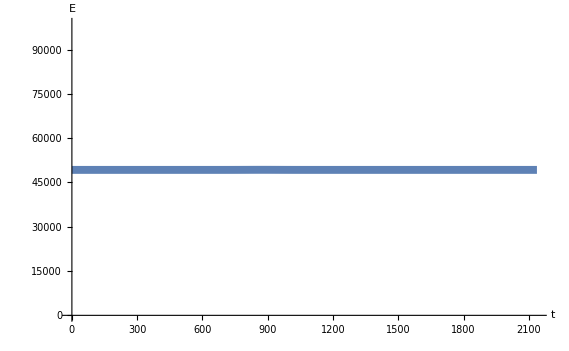

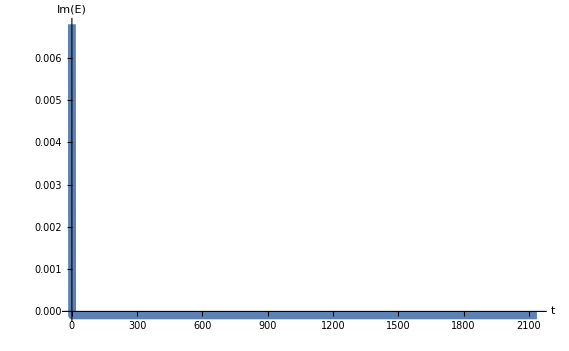

```mathematica
(*Energía: *)

EnerGraph = ListPlot[Transpose[{tLista,Re[Energy]}], PlotRange->{All,{0,2*Max[Re[Energy]]}},  AxesLabel->{"t", "E"}, AxesStyle->Large, Joined->True , Mesh->None, PlotStyle->{Thickness[0.01]}]
(*Grafico la parte compleja para ver que efectivamente puedo despreciarla: *)
ListPlot[Transpose[{tLista,Im[Energy]}],  AxesLabel->{"t", "Im(E)"}, AxesStyle->Large, Joined->True , Mesh->None, PlotStyle->{Thickness[0.01]}]

(*Energías:;
1. E = 6265.21 \pm 0.19;
2.i. E = 6265.20 \pm 0.01;
2.ii. E = 24231.6 \pm 0.8;
2.iii. E = 49257.55 \pm 14.45;
*)
```

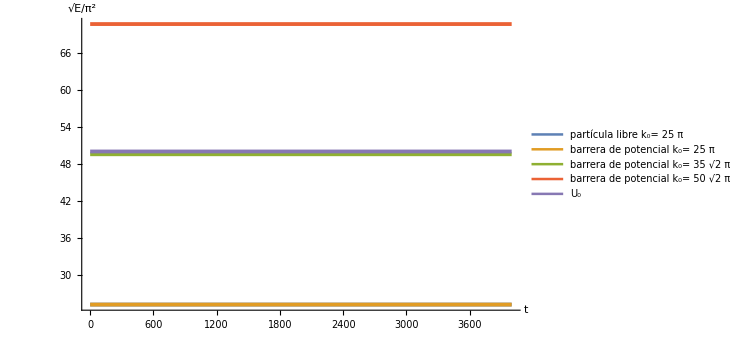

```mathematica
(*Grafico todas las gráficas de energía juntas*)
Nmin = 4000;
(*Valores medios de las energías*)
Es = Sqrt[{6265.21, 6265.20,24231.6, 49257.55 , 49272.}]/π;
U = Sqrt[((50*Pi)^2 )/π^2];
f0[x_]:=Es⟦1⟧;
f1[x_]:= Es⟦2⟧;
f2[x_] := Es⟦3⟧;
f3[x_] := Es⟦4⟧;
u[x_] := U;
ener1 = Plot[{f0[x],f1[x],f2[x],f3[x],u[x]},{x,0,Nmin},  PlotRange->{All,{0,All}}, AxesLabel->{"t", "√E/π^2"},AxesStyle->Large, ImageSize->550, PlotStyle->{Thickness[0.005]},PlotLegends->LineLegend[{"partícula libre \n k_0= 25 π","barrera de potencial \n k_0= 25 π", "barrera de potencial \n k_0= 35 √2 π", "barrera de potencial \n k_0= 50 √2 π", "U_0"},LabelStyle->{FontSize->20}]]
(*Aclaro por las dudas que estoy representando directamente rectas para el gráfico de las energías y no hay nada de ilegal en ello: me ocupé de revisar que en todos los casos se conserva la energía*)
```

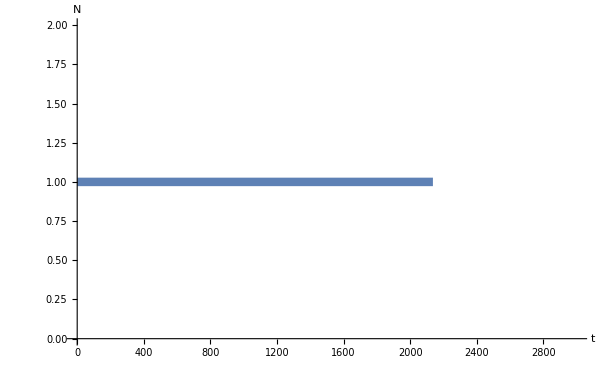

1

1

```mathematica
(*Norma: *)
ListPlot[Transpose[{tLista,Norma}], AxesLabel->{"t", "N"}, AxesStyle->Large, Joined->True , Mesh->None, PlotStyle->{Thickness[0.01]}, PlotRange->{{0,3000},{0,2}}]
```

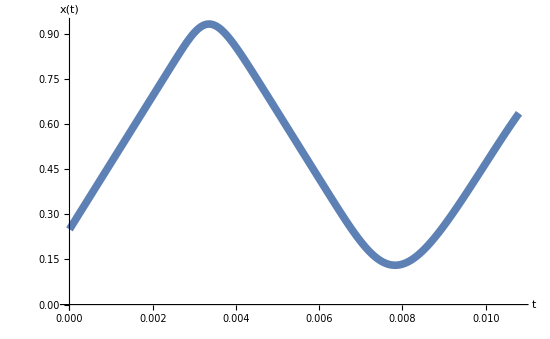

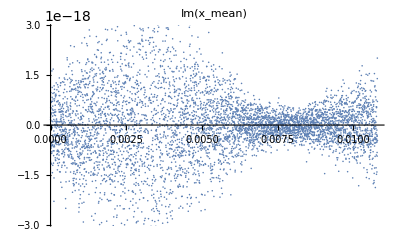

```mathematica
(*Posición: *)
ListPlot[Transpose[{tLista,Re[xMean]}],AxesLabel->{"t", "x(t)"}, AxesStyle->Large, Joined->True , Mesh->None, PlotStyle->{Thickness[0.01]}]
ListPlot[Transpose[{tLista,Im[xMean]}],AxesLabel->{"t", "Im[x(t)]"}, AxesStyle->Large, Joined->True , Mesh->None, PlotStyle->{Thickness[0.01]}]
(*La parte imaginaria tiene un comportamiento raro, pero aún así es despreciable dado que gira en torno a 10^-18*)
```

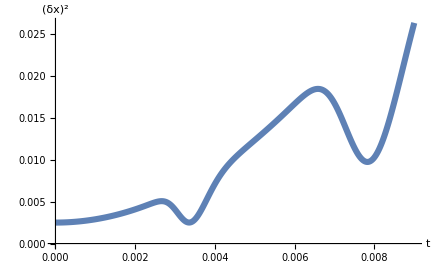

0.00249998

```mathematica
(*Varianza de x_: *)
ListPlot[Transpose[{tLista, xVar}], AxesLabel->{"t", "(δx)^2"}, AxesStyle->Large, Joined->True , Mesh->None, PlotStyle->{Thickness[0.01]}]
Min[xVar]
```

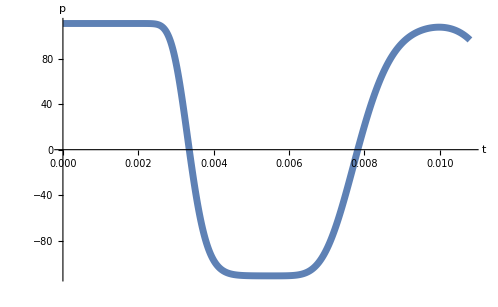

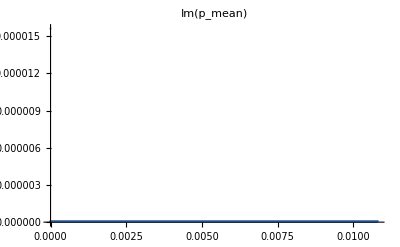

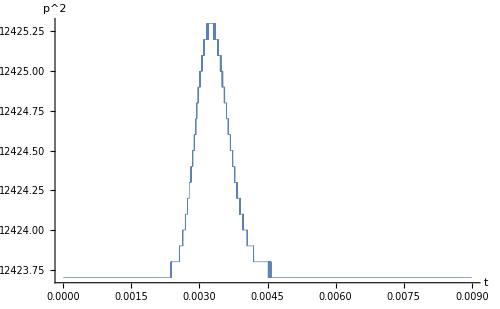

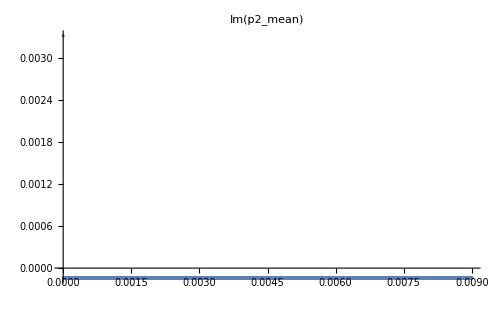

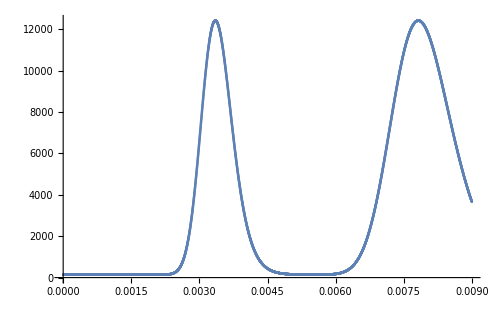

```mathematica
(*Momento: *)
ListPlot[Transpose[{tLista,Re[pMean]}], AxesLabel->{"t", "p"}, AxesStyle->Large, Joined->True , Mesh->None, PlotStyle->{Thickness[0.01]}]
ListPlot[Transpose[{tLista,Im[pMean]}], AxesLabel->{"t", "Im[p]"}, AxesStyle->Large, Joined->True , Mesh->None, PlotStyle->{Thickness[0.01]}]
```

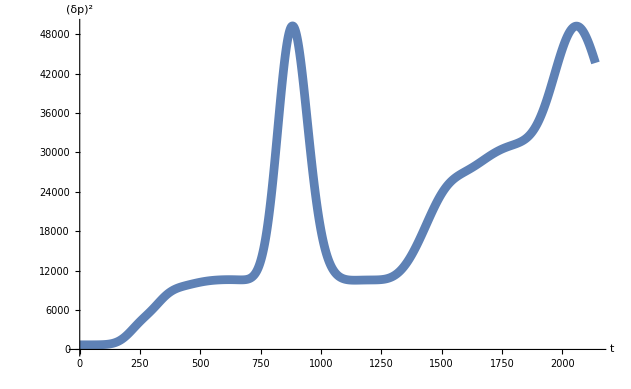

706.063

```mathematica
(*Varianza de momento: *)
ListPlot[Transpose[{tLista, pVar}],AxesLabel->{"t", "(δp)^2"}, AxesStyle->Large, Joined->True , Mesh->None, PlotStyle->{Thickness[0.01]}, PlotRange->All]
Min[pVar]
```

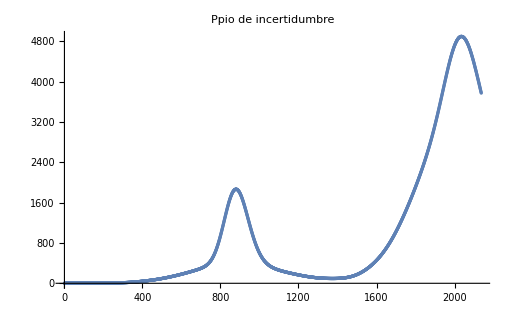

1.76332

```mathematica
(*Ppio de incertidumbre: xVar*pVar ≥ (nu/2)^2*)
incer = ConstantArray[0 ,Nt]; (*incertidumbre*)
Do[
incer⟦n⟧=xVar⟦n⟧*pVar⟦n⟧;
,{n,1,Nt}]
ListPlot[Transpose[{tLista,incer}], PlotLabel->"Ppio de incertidumbre"]
Print["Valor mínimo: ", Min[incer]]
```

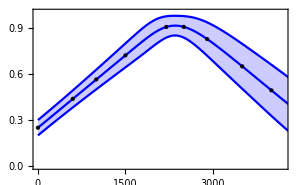
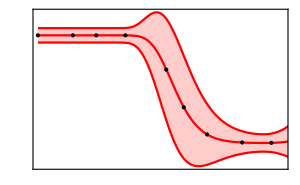

```mathematica
(*Gráfico conjunto de esperanzas*)
pVar = ConstantArray[0, Nt];
Do[pVar⟦n⟧ = Abs[p2Mean⟦n⟧] - Abs[pMean⟦n⟧]^2;,{n,1,Nt}];


opacity = 0.2;
imagesize = 300;
pointsize = Medium;
ns ={1,600,1000,1500,2200,2500,2900,3500,4000};
xUpp = Re[xMean] + Sqrt[Re[xVar]];
xDown = Re[xMean] - Sqrt[Re[xVar]];
xErrorGraph = ListLinePlot[{xUpp,xDown},Filling->{1->{2}},FillingStyle->{LightBlue,Opacity[opacity]},PlotStyle->Blue];
xMeanGraph = ListLinePlot[xMean, PlotStyle->Blue];
xcolorPoint = Black;
xMeanPoints ={Graphics[{PointSize[pointsize],xcolorPoint,Point[{tLista⟦ns⟦1⟧⟧,Re[xMean]⟦ns⟦1⟧⟧}]}],
 Graphics[{PointSize[pointsize],xcolorPoint,Point[{tLista⟦ns⟦2⟧⟧,Re[xMean]⟦ns⟦2⟧⟧}]}],
 Graphics[{PointSize[pointsize],xcolorPoint,Point[{tLista⟦ns⟦3⟧⟧,Re[xMean]⟦ns⟦3⟧⟧}]}],
 Graphics[{PointSize[pointsize],xcolorPoint,Point[{tLista⟦ns⟦4⟧⟧,Re[xMean]⟦ns⟦4⟧⟧}]}],
 Graphics[{PointSize[pointsize],xcolorPoint,Point[{tLista⟦ns⟦5⟧⟧,Re[xMean]⟦ns⟦5⟧⟧}]}],
 Graphics[{PointSize[pointsize],xcolorPoint,Point[{tLista⟦ns⟦6⟧⟧,Re[xMean]⟦ns⟦6⟧⟧}]}],
 Graphics[{PointSize[pointsize],xcolorPoint,Point[{tLista⟦ns⟦7⟧⟧,Re[xMean]⟦ns⟦7⟧⟧}]}],
 Graphics[{PointSize[pointsize],xcolorPoint,Point[{tLista⟦ns⟦8⟧⟧,Re[xMean]⟦ns⟦8⟧⟧}]}],
 Graphics[{PointSize[pointsize],xcolorPoint,Point[{tLista⟦ns⟦9⟧⟧,Re[xMean]⟦ns⟦9⟧⟧}]}]};
plot1 = Show[{xErrorGraph, xMeanGraph, xMeanPoints}, PlotRange->{{0,4200},{0,1}},ImagePadding->25,Frame->{True,True,True,False},FrameStyle->{Automatic,Blue,Automatic,Automatic},PlotStyle->Opacity[0.2],ImageSize->imagesize];
(*ns para cada inciso:;
ns1 = {1,600,1000,1500,2200,2500,2900,3500,4000};
ns2i ={1,150,300,450,600,850,1000,1150,1350};
ns2ii ={1,150,220,290,370,500,600,700,850};
ns2iii ={1,100,170,240,310,380,450,520, 590};
*)

(*Para el momento normalizo todo a p0 = pMean[t = 0]*)
pUpp = (Re[pMean] +Sqrt[ Re[pVar]])/Re[pMean⟦1⟧];
pDown = (Re[pMean] - Sqrt[Re[pVar]])/Re[pMean⟦1⟧];
pErrorGraph = ListLinePlot[{pUpp,pDown},Filling->{1->{2}},FillingStyle->{LightRed,Opacity[opacity]},PlotStyle->Red];
pMeanGraph = ListLinePlot[Re[pMean]/Re[pMean⟦1⟧], PlotStyle->Red];
pcolorPoint = Black;
pMeanPoints ={Graphics[{PointSize[pointsize],pcolorPoint,Point[{tLista⟦ns⟦1⟧⟧,Re[pMean]⟦ns⟦1⟧⟧/Re[pMean⟦1⟧]}]}],
 Graphics[{PointSize[pointsize],pcolorPoint,Point[{tLista⟦ns⟦2⟧⟧,Re[pMean]⟦ns⟦2⟧⟧/Re[pMean⟦1⟧]}]}],
 Graphics[{PointSize[pointsize],pcolorPoint,Point[{tLista⟦ns⟦3⟧⟧,Re[pMean]⟦ns⟦3⟧⟧/Re[pMean⟦1⟧]}]}],
 Graphics[{PointSize[pointsize],pcolorPoint,Point[{tLista⟦ns⟦4⟧⟧,Re[pMean]⟦ns⟦4⟧⟧/Re[pMean⟦1⟧]}]}],
 Graphics[{PointSize[pointsize],pcolorPoint,Point[{tLista⟦ns⟦5⟧⟧,Re[pMean]⟦ns⟦5⟧⟧/Re[pMean⟦1⟧]}]}],
 Graphics[{PointSize[pointsize],pcolorPoint,Point[{tLista⟦ns⟦6⟧⟧,Re[pMean]⟦ns⟦6⟧⟧/Re[pMean⟦1⟧]}]}],
 Graphics[{PointSize[pointsize],pcolorPoint,Point[{tLista⟦ns⟦7⟧⟧,Re[pMean]⟦ns⟦7⟧⟧/Re[pMean⟦1⟧]}]}],
 Graphics[{PointSize[pointsize],pcolorPoint,Point[{tLista⟦ns⟦8⟧⟧,Re[pMean]⟦ns⟦8⟧⟧/Re[pMean⟦1⟧]}]}],
 Graphics[{PointSize[pointsize],pcolorPoint,Point[{tLista⟦ns⟦9⟧⟧,Re[pMean]⟦ns⟦9⟧⟧/Re[pMean⟦1⟧]}]}]};
plot2 =Show[{pErrorGraph, pMeanGraph, pMeanPoints}, PlotRange->{{0,4200},All},ImagePadding->25,Axes->False,Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Red},ImageSize->imagesize,AxesStyle->Large];

Overlay[{plot1,plot2}]
```